```mathematica
Import["C:\\Users\\douwm\\repos\\ca_compression\\functions_to_find_compression_rules.wl"]
```

```mathematica
nRules = numberOfGeneralRules[#]&/@Range[1,6]
```

{256,4294967296,340282366920938463463374607431768211456,13407807929942597099574024998205846127479365820592393377723561443721764030073546976801874298166903427690031858186486050853753882811946569946433649006084096,32317006071311007300714876688669951960444102669715484032130345427524655138867890893197201411522913463688717960921898019494119559150490921095088152386448283120630877367300996091750197750389652106796057638384067568276792218642619756161838094338476170470581645852036305042887575891541065808607552399123930385521914333389668342420684974786564569494856176035326322058077805659331026192708460314150258592864177116725943603718461857357598351152301645904403697613233287231227125684710820209725157101726931323469678542580656697935045997268352998638215525166389437335543602135433229604645318478604952148193555853611059596230656,1090748135619415929462984244733782862448264161996232692431832786189721331849119295216264234525201987223957291796157025273109870820177184063610979765077554799078906298842192989538609825228048205159696851613591638196771886542609324560121290553901886301017900252535799917200010079600026535836800905297805880952350501630195475653911005312364560014847426035293551245843928918752768696279344088055617515694349945406677825140814900616105920256438504578013326493565836047242407382442812245131517757519164899226365743722432277368075027627883045206501792761700945699168497257879683851737049996900961120515655050115561271491492515342105748966629547032786321505730828430221664970324396138635251626409516168005427623435996308921691446181187406395310665404885739434832877428167407495370993511868756359970390117021823616749458620969857006263612082706715408157066575137281027022310927564910276759160520878304632411049364568754920967322982459184763427383790272448438018526977764941072715611580434690827459339991961414242741410599117426060556483763756314527611362658628383368621157993638020878537675545336789915694234433955666315070087213535470255670312004130725495834508357439653828936077080978550578912967907352780054935621561090795845172954115972927479877527738560008204118558930004777748727761853813510493840581861598652211605960308356405941821189714037868726219481498727603653616298856174822413033485438785324024751419417183012281078209729303537372804574372095228703622776363945290869806258422355148507571039619387449629866808188769662815778153079393179093143648340761738581819563002994422790754955061288818308430079648693232179158765918035565216157115402992120276155607873107937477466841528362987708699450152031231862594203085693838944657061346236704234026821102958954951197087076546186622796294536451620756509351018906023773821539532776208676978589731966330308893304665169436185078350641568336944530051437491311298834367265238595404904273455928723949525227184617404367854754610474377019768025576605881038077270707717942221977090385438585844095492116099852538903974655703943973086090930596963360767529964938414598185705963754561497355827813623833288906309004288017321424808663962671333528009232758350873059614118723781422101460198615747386855096896089189180441339558524822867541113212638793675567650340362970031930023397828465318547238244232028015189689660418822976000815437610652254270163595650875433851147123214227266605403581781469090806576468950587661997186505665475715792896}

```mathematica
SetSharedFunction[PSow]; (*Allows you to Sow in parallel*)
PSow[x_]:=Sow[x];
```

```mathematica
testRandomRule[]:=(
dataDimensionality = RandomInteger[{2,6}];
ruleRange = RandomInteger[{1,6}];
ruleNumber = RandomInteger[nRules[[ruleRange]]-1];
startTime = RandomInteger[{1,10}];
res = testRuleRangeStartDimForReduction[ruleNumber,ruleRange,startTime,dataDimensionality];
If[res >0.01, PSow[{dataDimensionality,ruleRange,startTime,ruleNumber,res}]]
)
```

```mathematica
dataDimensionality = RandomInteger[{2,6}];
ruleRange = RandomInteger[{1,6}];
ruleNumber = RandomInteger[nRules[[ruleRange]]-1];
startTime = RandomInteger[{1,10}];
```

{{6,6,6,6,6},{6,6,6,6,6},{6,6,6,6,6},{2,4,4,3,4},{6,6,6,6,6},{6,6,6,6,6},{4,4,3,4,2},{6,6,6,6,6},{6,6,6,6,6},{6,6,6,6,6},{6,6,6,6,6},{6,6,6,6,6},{4,3,4,2,4},{6,6,6,6,6},{6,6,6,6,6},{6,6,6,6,6},{6,6,6,6,6},{4,2,4,4,3},{6,6,6,6,6},{6,6,6,6,6},{6,6,6,6,6},{6,6,6,6,6},{6,6,6,6,6},{6,6,6,6,6},{3,4,2,4,4},{6,6,6,6,6},{6,6,6,6,6},{6,6,6,6,6},{6,6,6,6,6},{6,6,6,6,6},{6,6,6,6,6},{6,6,6,6,6}}

```mathematica
testRandomRule[]
```

Last::normal: Nonatomic expression expected at position 1 in Last[splitup].

First::normal: Nonatomic expression expected at position 1 in First[splitup].

First::normal: Nonatomic expression expected at position 1 in First[testperm].

First::normal: Nonatomic expression expected at position 1 in First[8].

General::stop: Further output of First::normal will be suppressed during this calculation.

If[0.125 First[8.]>0.01,PSow[{dataDimensionality,ruleRange,startTime,ruleNumber,res}]]

```mathematica
res = Last@Reap[ParallelDo[testRandomRule[],{10}]]
(*Save["betterthan046_20210312",res];*)
```

{{{2,1,6,84,0.25},{4,6,4,420311070641550788293926533325780708833902923597376687820016839010481282981574440801673633873219016791194713614451386282492995744814453816376797541805353211323607227510167527824332238839785325316338773049835651810469393109995811017983930273950723130647068472083410708987897548890483396353735796859829464637646908280290058545696827989066279561483574112618835529452146474048843770316213832434145386041034802979901240919556899178132916338690519556510998219327351943649662715041630696793177140030853823916188163124702406220110438249567151651877075082633028598654451695434314663479967926687814366054089793025799581756294810052867262099756695286239472117637038753970207316877236267141886353459977810713879210207256056581635104137039997117175087181652413349610041187151830427108225155755431919289018542767367337522128454774488904003634215572542296976065737274027830725650611452895039190476923092778756737890966491644746490917231551739912024415971763128236631323831638652042867366728959890918862787508499777187216224376642661854330272344512542190193858694612648499381218715699046005171980491057140278337533779434181184917962782128126843519778418858738797512105859896841026604386452163285829163217523539856264407791713361529887792018534280934558375344072531919980219309401889838551355780444208957711582178871039541576670784680160938283238913319695364426923034583984903468070631653713237490638172085671885176947486368577068086188273519836932988536593737532613305900673278977706708565180041947653216225512303263740413848061193160124280068156621140664241668321536467448576889972615902191828022555695788700104885816360502894028291617277498556190843423963625013874849790823665754728458149575113621378523709205549339654645087801511218589697434035907580642935510287131828227268306083588055260092989322966907207135811505167263320696521681853407905748482983401155681591126414988253213952105080856640072355972172868308650746162235932932320779144608667895419856988532801416536211763965105141117056994347338352653191621886235167573421434484480817504869140749168470175653240509369365238080899606170807790502735428587634021078520053987000805223001022757772195834591153264734650244147753570113605810884747938187128724953731866490174331703520645923578449906233481071854894371158532012519214643487098399190481449652653691470868073945550150013165549711410461513716767265274841949574416479928807471129066738382872176611562101686647440162191945017183328658521195904699025220958529345443670718318,0.125},{6,3,2,202340537631311095315605712620590947596,0.0625},{5,3,1,293482990264173877976201978709289252262,0.0625},{5,1,5,7,0.09375},{2,1,7,75,0.25}}}

```mathematica
testRandomRule[]
```

```mathematica
bt46 = First@Get["betterthan046"];
```

```mathematica
Dimensions[bt46]
```

{241,5}

```mathematica
Count[#,Max[#]]&@bt46[[All,5]]
```

1

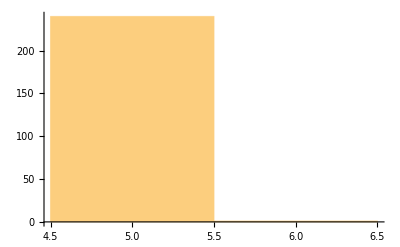
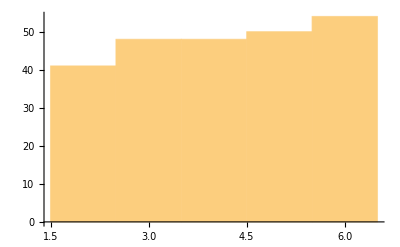
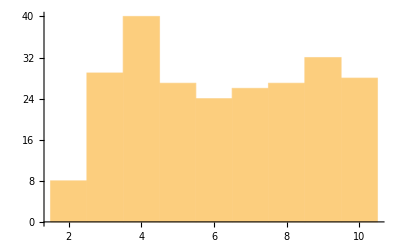
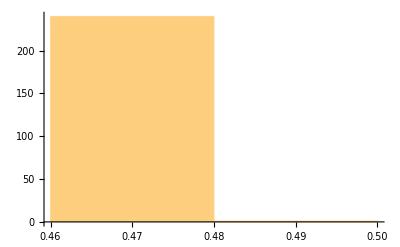

```mathematica
Histogram/@Transpose@bt46[[All,{1,2,3,5}]]
```

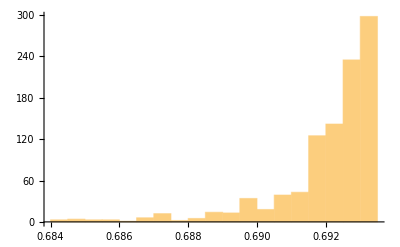

```mathematica
Histogram[Table[Entropy[RandomInteger[{0,1},500]]//N,1000]]
```

```mathematica
Entropy[{0,1,0,0,0}]//N
```

0.500402

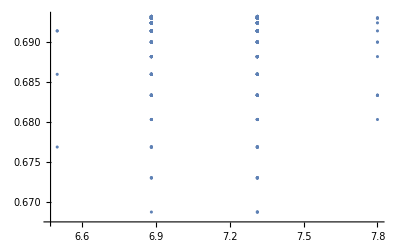

```mathematica
ListPlot[Table[With[{a = RandomInteger[{0,1},100]},
{ByteCount@a/ByteCount@Compress@a,Entropy[a]}],500]]
```

```mathematica
With[{a=RandomInteger[{0,1},4],N[ByteCount[a]/ByteCount[Compress[a]]]]
```

```mathematica
With[{a=3,b=3*a},c=5*a]
```

15

```mathematica
dataDim = 5 (*RandomInteger[{2,7}];*);
ruleRange = RandomInteger[{1,6}];
ruleNumber = RandomInteger[nRules[[ruleRange]]-1];
startTime = RandomInteger[{1,10}];
evolutions = getEvolutionsForAllPermutations[ruleNumber, ruleRange,startTime,dataDim];
(*ArrayPlot/@evolutions*)
noutdep = numberOfUpdatesToDistinguishEachPermutation[evolutions,dataDim];
noutdep//Column;
f = fractionOfPermutationsDistinguishable[noutdep,{-100,-2,-1,0,1,2}];
ent = entropyForEachPermutationEvolution[evolutions,dataDim-1];
aveEntForReadIndex = Total[ent,{1}]/Length[ent]
AverageEntropy[evolutions,{0,-1}]
```

{0.484291,0.484291,0.484291,0.484291,0.484291}

{0.555432,0.484291}

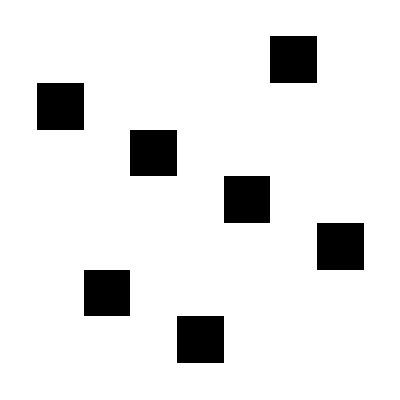

{{0,1,0,0,0,0,0},{0,0,0,0,0,1,0},{0,0,1,0,0,0,0},{0,0,0,0,0,0,1},{0,0,0,1,0,0,0},{1,0,0,0,0,0,0},{0,0,0,0,1,0,0}}

{{0,1,0,0,0,0,0},{0,0,0,0,0,1,0},{0,0,1,0,0,0,0},{0,0,0,0,0,0,1},{0,0,0,1,0,0,0},{1,0,0,0,0,0,0},{0,0,0,0,1,0,0}}

```mathematica
perm = 2;
permevol = evolutions[[perm]];
ArrayPlot@permevol
cols = #&/@Transpose[permevol]
seqlength = 7;
seq = #[[1;;seqlength]]&/@cols
entropyForSeq = Entropy/@seq//N
```

```mathematica
ent = entropyForEachPermutationEvolution[evolutions,dataDim-1];
aveEntForReadIndex = Total[ent,{1}]/Length[ent]
```

{0.306465,0.306465,0.306465,0.306465,0.306465,0.306465,0.306465}

```mathematica
Length[ent]
```

128